```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"]
```

```mathematica
niceStyle={
Axes->True,
Frame->True,
GridLines->Automatic,
ImageSize->600,
ImageMargins->3,
LabelStyle->{"Arial",16,Bold},
BaseStyle->{FontFamily->"Arial",FontSize->16},
FrameTicksStyle->{Directive[16,Plain],Directive[16,Plain]},
FrameStyle->Thick,
GridLinesStyle->Directive[Dashed,Gray],
AxesStyle->Directive[Thick,Dashed],
FrameLabel->{"V_bias [V]","Amplitude [V]"}
};
niceStyle2={
Axes->True,
Frame->True,
GridLines->Automatic,
ImageSize->600,
ImageMargins->3,
LabelStyle->{"Arial",16,Bold},
BaseStyle->{FontFamily->"Arial",FontSize->16},
FrameTicksStyle->{Directive[16,Plain],Directive[16,Plain]},
FrameStyle->Thick,
GridLinesStyle->Directive[Dashed,Gray],
AxesStyle->Directive[Thick,Dashed],
FrameLabel->{"V_bias [V]","Distance [m]"}
};
```

## Import Data

```mathematica
ResDat=ReadList["resonance_onlydata.txt",{Real,Real,Real,Real}];
ResDat1=Replace[Drop[ResDat,None,-2],{f_,V_}->{10^-3 f,V},2];(*Hz->kHz*)
ResDat2=Replace[Drop[ResDat,None,2],{f_,V_}->{10^-3 f,V},2];(*Hz->kHz*)
```

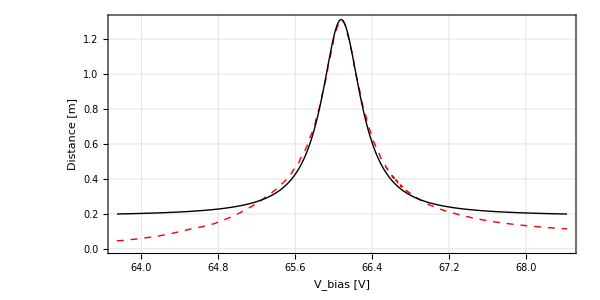

```mathematica
ListLinePlot[{ResDat1,ResDat2},niceStyle2,FrameLabel->{"Frequency [kHz]","Amplitude [V]"},PlotStyle->{{Red,Dashed,Thick},{Black,Thick}},AspectRatio->1/2]
```

### IV-Curves AU on C without feedback

```mathematica
Au10IVTemp=ReadList["Au_0010.iv.cur",{Real,Real,Real,Real}];
Au10IVFwd=Drop[Au10IVTemp,None,-2];
Au10IVBwd=Drop[Au10IVTemp,None,2];
```

```mathematica
Au14IVTemp=ReadList["Au_0014.iv.cur",{Real,Real,Real,Real}];
Au14IVFwd=Drop[Au14IVTemp,None,-2];
Au14IVBwd=Drop[Au14IVTemp,None,2];
```

```mathematica
Au18IVTemp=ReadList["Au_0018.iv.cur",{Real,Real,Real,Real}];
Au18IVFwd=Drop[Au18IVTemp,None,-2];
Au18IVBwd=Drop[Au18IVTemp,None,2];
```

### IV-Curves C without feedback

```mathematica
C22IVTemp=ReadList["C_0022.iv.cur",{Real,Real,Real,Real}];
C22IVFwd=Drop[C22IVTemp,None,-2];
C22IVBwd=Drop[C22IVTemp,None,2];
```

```mathematica
C26IVTemp=ReadList["C_0026.iv.cur",{Real,Real,Real,Real}];
C26IVFwd=Drop[C26IVTemp,None,-2];
C26IVBwd=Drop[C26IVTemp,None,2];
```

```mathematica
C30IVTemp=ReadList["C_0030.iv.cur",{Real,Real,Real,Real}];
C30IVFwd=Drop[C30IVTemp,None,-2];
C30IVBwd=Drop[C30IVTemp,None,2];
```

### IV-Curves AU on C with feedback

```mathematica
Au87IVTemp=ReadList["Au_0087.iv.cur",{Real,Real,Real,Real}];
Au87IVFwd=Drop[Au87IVTemp,None,-2];
Au87IVBwd=Drop[Au87IVTemp,None,2];
```

```mathematica
Au97IVTemp=ReadList["Au_0097.iv.cur",{Real,Real,Real,Real}];
Au97IVFwd=Drop[Au97IVTemp,None,-2];
Au97IVBwd=Drop[Au97IVTemp,None,2];
```

```mathematica
Au107IVTemp=ReadList["Au_0107.iv.cur",{Real,Real,Real,Real}];
Au107IVFwd=Drop[Au107IVTemp,None,-2];
Au107IVBwd=Drop[Au107IVTemp,None,2];
```

### IV-Curves C with feedback

```mathematica
C57IVTemp=ReadList["C_0057.iv.cur",{Real,Real,Real,Real}];
C57IVFwd=Drop[C57IVTemp,None,-2];
C57IVBwd=Drop[C57IVTemp,None,2];
```

```mathematica
C67IVTemp=ReadList["C_0067.iv.cur",{Real,Real,Real,Real}];
C67IVFwd=Drop[C67IVTemp,None,-2];
C67IVBwd=Drop[C67IVTemp,None,2];
```

```mathematica
C77IVTemp=ReadList["C_0077.iv.cur",{Real,Real,Real,Real}];
C77IVFwd=Drop[C77IVTemp,None,-2];
C77IVBwd=Drop[C77IVTemp,None,2];
```

## Fitting IV-Curves without feedback

### Gold on Graphite

#### Gold 1: Au_0010

```mathematica
ListPlot[{Au10IVFwd,Au10IVBwd}];
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0234685 | 0.000180505 | 130.015 | 7.74368×10^-132
b | -0.614425 | 0.0010309 | -596.007 | 1.13212×10^-211
V0 | -0.107014 | 0.00329999 | -32.4285 | 1.6134×10^-61

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0212355 | 0.000131183 | 161.878 | 1.756×10^-257
b | -0.600975 | 0.000531376 | -1130.98 | 1.44505236528478×10^-470
V0 | -0.113927 | 0.00485497 | -23.466 | 1.92644×10^-65

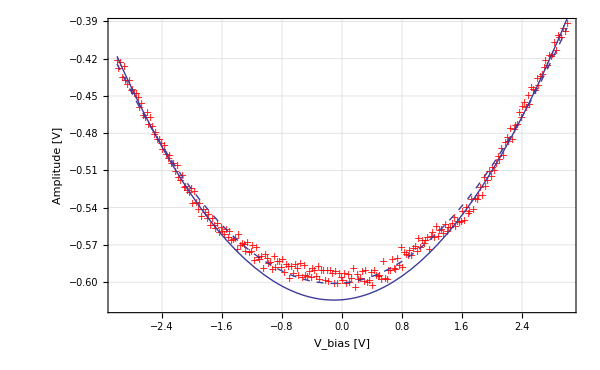

```mathematica
Au10IVFwdEdge=Drop[Au10IVFwd,{Position[Au10IVFwd,-1.5411764383316][[1,1]],
Position[Au10IVFwd,1.5411764383316][[1,1]]}];
ListPlot[Au10IVFwdEdge];
FitU0Au10Fwd=NonlinearModelFit[Au10IVFwdEdge,a(x-V0)^2+b,{a,b,V0},x];
FitU0Au10Fwd2=NonlinearModelFit[Au10IVFwd,a(x-V0)^2+b,{a,b,V0},x];
FitU0Au10Fwd["ParameterTable"]
FitU0Au10Fwd2["ParameterTable"]
Show[ListPlot[Au10IVFwd,PlotMarkers->{"+"},PlotStyle->Red],Plot[Normal[FitU0Au10Fwd],{x,-3,3},PlotStyle->{Thick}],Plot[Normal[FitU0Au10Fwd2],{x,-3,3},PlotStyle->{Thick,Dashed}],niceStyle,AxesOrigin->{-3,-.65}]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.023171 | 0.000201695 | 114.882 | 2.18794×10^-125
b | -0.612366 | 0.00115139 | -531.85 | 1.08781×10^-205
V0 | -0.120152 | 0.00376486 | -31.914 | 9.13755×10^-61

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0210298 | 0.000128679 | 163.428 | 1.61017×10^-258
b | -0.59947 | 0.000521075 | -1150.45 | 1.92669063952488×10^-472
V0 | -0.125592 | 0.00481977 | -26.0578 | 1.35295×10^-73

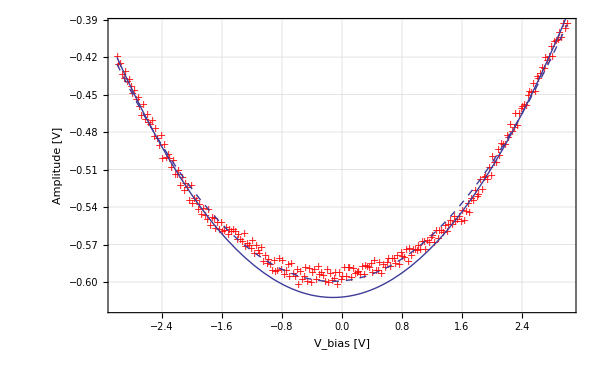

```mathematica
Au10IVBwdEdge=Drop[Au10IVBwd,{Position[Au10IVBwd,-1.5411764383316][[1,1]],
Position[Au10IVBwd,1.5411764383316][[1,1]]}];
ListPlot[Au10IVBwdEdge];
FitU0Au10Bwd=NonlinearModelFit[Au10IVBwdEdge,a(x-V0)^2+b,{a,b,V0},x];
FitU0Au10Bwd["ParameterTable"]
FitU0Au10Bwd2=NonlinearModelFit[Au10IVBwd,a(x-V0)^2+b,{a,b,V0},x];
FitU0Au10Bwd2["ParameterTable"]
Show[ListPlot[Au10IVBwd,PlotMarkers->{"+"},PlotStyle->Red],Plot[Normal[FitU0Au10Bwd],{x,-3,3},PlotStyle->{Thick}],Plot[Normal[FitU0Au10Bwd2],{x,-3,3},PlotStyle->{Thick,Dashed}],niceStyle,AxesOrigin->{-3,-.62}]
```

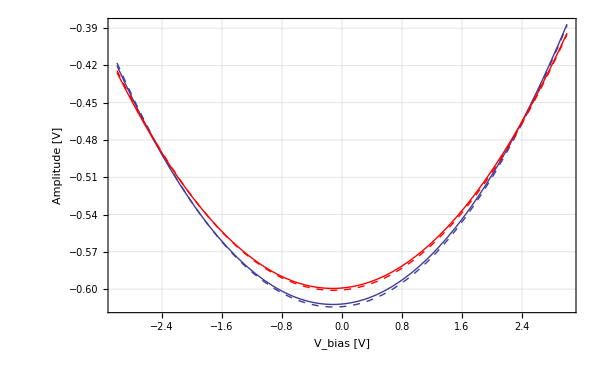

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0234685 | 0.000180505 | 130.015 | 7.74368×10^-132
b | -0.614425 | 0.0010309 | -596.007 | 1.13212×10^-211
V0 | -0.107014 | 0.00329999 | -32.4285 | 1.6134×10^-61

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0212355 | 0.000131183 | 161.878 | 1.756×10^-257
b | -0.600975 | 0.000531376 | -1130.98 | 1.44505236528478×10^-470
V0 | -0.113927 | 0.00485497 | -23.466 | 1.92644×10^-65

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.023171 | 0.000201695 | 114.882 | 2.18794×10^-125
b | -0.612366 | 0.00115139 | -531.85 | 1.08781×10^-205
V0 | -0.120152 | 0.00376486 | -31.914 | 9.13755×10^-61

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0210298 | 0.000128679 | 163.428 | 1.61017×10^-258
b | -0.59947 | 0.000521075 | -1150.45 | 1.92669063952488×10^-472
V0 | -0.125592 | 0.00481977 | -26.0578 | 1.35295×10^-73

```mathematica
Show[Plot[Normal[FitU0Au10Bwd],{x,-3,3},PlotRange->All],Plot[Normal[FitU0Au10Fwd],{x,-3,3},PlotStyle->Dashed],Plot[Normal[FitU0Au10Bwd2],{x,-3,3},PlotRange->All,PlotStyle->{Red}],Plot[Normal[FitU0Au10Fwd2],{x,-3,3},PlotStyle->{Red,Dashed}],niceStyle,AxesOrigin->{-3,-.61}]
FitU0Au10Fwd["ParameterTable"]
FitU0Au10Fwd2["ParameterTable"]
FitU0Au10Bwd["ParameterTable"]
FitU0Au10Bwd2["ParameterTable"]
```

#### Gold 2: Au_0014

```mathematica
ListPlot[{Au14IVFwd,Au14IVBwd}];
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0259277 | 0.000186709 | 138.867 | 4.05993×10^-156
b | -0.614548 | 0.000985494 | -623.594 | 1.76697×10^-250
V0 | -0.160002 | 0.00372544 | -42.9486 | 2.37516×10^-84

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0242651 | 0.000140396 | 172.833 | 1.29959×10^-264
b | -0.604942 | 0.000567784 | -1065.44 | 5.21663138701104×10^-464
V0 | -0.166338 | 0.00460099 | -36.1527 | 6.33857×10^-102

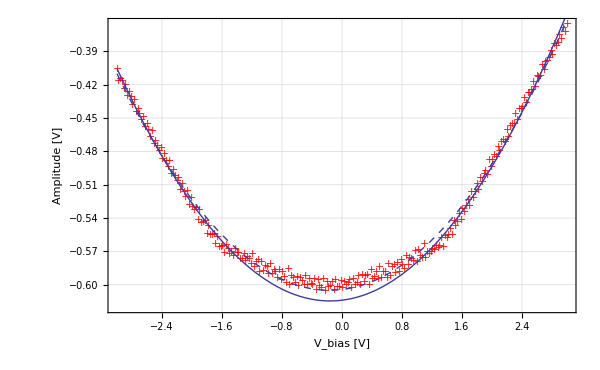

```mathematica
Au14IVFwdEdge=Drop[Au14IVFwd,{Position[Au14IVFwd,-1.25882351398468][[1,1]],
Position[Au14IVFwd,1.25882351398468][[1,1]]}];
ListPlot[Au14IVFwdEdge];
FitU0Au14Fwd=NonlinearModelFit[Au14IVFwdEdge,a(x-V0)^2+b,{a,b,V0},x];
FitU0Au14Fwd["ParameterTable"]
FitU0Au14Fwd2=NonlinearModelFit[Au14IVFwd,a(x-V0)^2+b,{a,b,V0},x];
FitU0Au14Fwd2["ParameterTable"]
Show[ListPlot[Au14IVFwd,PlotMarkers->{"+"},PlotStyle->Red],Plot[Normal[FitU0Au14Fwd],{x,-3,3},PlotStyle->Thick],Plot[Normal[FitU0Au14Fwd2],{x,-3,3},PlotStyle->{Dashed,Thick}],niceStyle,AxesOrigin->{-3,-.65}]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0258871 | 0.000192523 | 134.462 | 4.19575×10^-154
b | -0.614076 | 0.00101662 | -604.038 | 1.79042×10^-248
V0 | -0.151122 | 0.00382757 | -39.4825 | 1.81783×10^-79

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0242532 | 0.000144785 | 167.512 | 3.31145×10^-261
b | -0.604671 | 0.000585759 | -1032.29 | 1.54960888858702×10^-460
V0 | -0.155367 | 0.00473388 | -32.8203 | 3.67848×10^-93

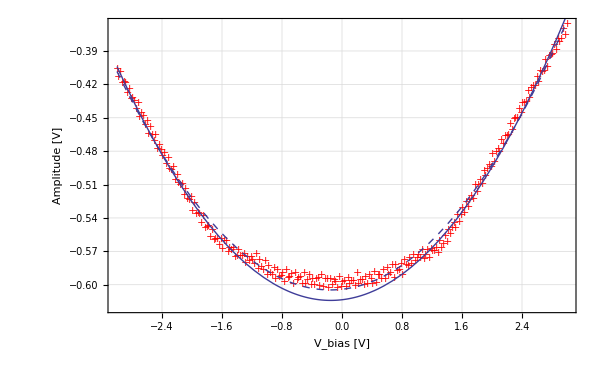

```mathematica
Au14IVBwdEdge=Drop[Au14IVBwd,{Position[Au14IVBwd,-1.25882351398468][[1,1]],
Position[Au14IVBwd,1.25882351398468][[1,1]]}];
ListPlot[Au14IVBwdEdge];
FitU0Au14Bwd=NonlinearModelFit[Au14IVBwdEdge,a(x-V0)^2+b,{a,b,V0},x];
FitU0Au14Bwd["ParameterTable"]
FitU0Au14Bwd2=NonlinearModelFit[Au14IVBwd,a(x-V0)^2+b,{a,b,V0},x];
FitU0Au14Bwd2["ParameterTable"]
Show[ListPlot[Au14IVBwd,PlotMarkers->{"+"},PlotStyle->Red],Plot[Normal[FitU0Au14Bwd],{x,-3,3},PlotStyle->Thick],Plot[Normal[FitU0Au14Bwd2],{x,-3,3},PlotStyle->{Dashed,Thick}],niceStyle,AxesOrigin->{-3,-.65}]
```

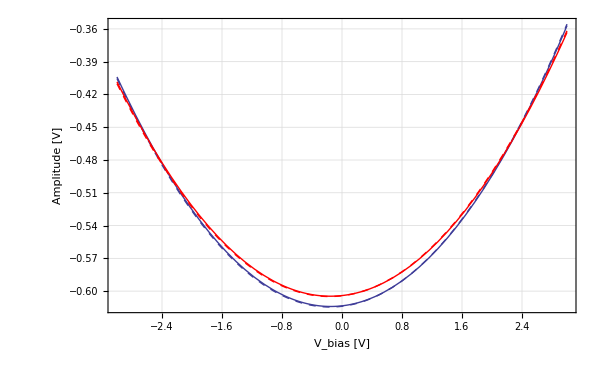

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0259277 | 0.000186709 | 138.867 | 4.05993×10^-156
b | -0.614548 | 0.000985494 | -623.594 | 1.76697×10^-250
V0 | -0.160002 | 0.00372544 | -42.9486 | 2.37516×10^-84

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0242651 | 0.000140396 | 172.833 | 1.29959×10^-264
b | -0.604942 | 0.000567784 | -1065.44 | 5.21663138701104×10^-464
V0 | -0.166338 | 0.00460099 | -36.1527 | 6.33857×10^-102

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0258871 | 0.000192523 | 134.462 | 4.19575×10^-154
b | -0.614076 | 0.00101662 | -604.038 | 1.79042×10^-248
V0 | -0.151122 | 0.00382757 | -39.4825 | 1.81783×10^-79

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0242532 | 0.000144785 | 167.512 | 3.31145×10^-261
b | -0.604671 | 0.000585759 | -1032.29 | 1.54960888858702×10^-460
V0 | -0.155367 | 0.00473388 | -32.8203 | 3.67848×10^-93

```mathematica
Show[Plot[Normal[FitU0Au14Bwd],{x,-3,3},PlotRange->All],Plot[Normal[FitU0Au14Fwd],{x,-3,3},PlotStyle->Dashed],
Plot[Normal[FitU0Au14Bwd2],{x,-3,3},PlotStyle->Red],Plot[Normal[FitU0Au14Fwd2],{x,-3,3},PlotStyle->{Red,Dashed}],niceStyle,AxesOrigin->{-3,-.61}]
FitU0Au14Fwd["ParameterTable"]
FitU0Au14Fwd2["ParameterTable"]
FitU0Au14Bwd["ParameterTable"]
FitU0Au14Bwd2["ParameterTable"]
```

#### Gold 3: Au_0018

```mathematica
ListPlot[{Au18IVFwd,Au18IVBwd}];
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0251697 | 0.000190925 | 131.831 | 1.46337×10^-132
b | -0.621748 | 0.00108905 | -570.907 | 2.06113×10^-209
V0 | -0.139716 | 0.00332511 | -42.0186 | 5.06111×10^-74

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0228869 | 0.000144262 | 158.648 | 2.7364×10^-255
b | -0.608378 | 0.00058382 | -1042.06 | 1.42800357367137×10^-461
V0 | -0.146103 | 0.00498724 | -29.2954 | 2.86083×10^-83

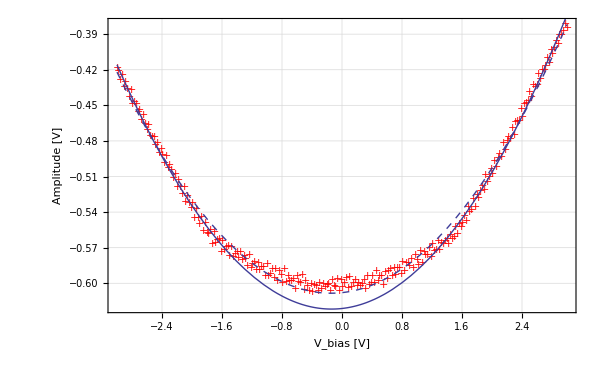

```mathematica
Au18IVFwdEdge=Drop[Au18IVFwd,{Position[Au18IVFwd,-1.5411764383316][[1,1]],
Position[Au18IVFwd,1.5411764383316][[1,1]]}];
ListPlot[Au18IVFwdEdge];
FitU0Au18Fwd=NonlinearModelFit[Au18IVFwdEdge,a(x-V0)^2+b,{a,b,V0},x];
FitU0Au18Fwd2=NonlinearModelFit[Au18IVFwd,a(x-V0)^2+b,{a,b,V0},x];
FitU0Au18Fwd["ParameterTable"]
FitU0Au18Fwd2["ParameterTable"]
Show[ListPlot[Au18IVFwd,PlotMarkers->{"+"},PlotStyle->Red],Plot[Normal[FitU0Au18Fwd],{x,-3,3},PlotStyle->Thick],Plot[Normal[FitU0Au18Fwd2],{x,-3,3},PlotStyle->{Thick,Dashed}],niceStyle,AxesOrigin->{-3,-.65}]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.025169 | 0.000204232 | 123.238 | 4.80242×10^-129
b | -0.621341 | 0.00116524 | -533.231 | 7.9485×10^-206
V0 | -0.134066 | 0.00354262 | -37.8437 | 6.56448×10^-69

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0228566 | 0.00015016 | 152.215 | 8.67667×10^-251
b | -0.6078 | 0.000607826 | -999.957 | 4.84805865718675×10^-457
V0 | -0.138838 | 0.00518941 | -26.7541 | 1.0054×10^-75

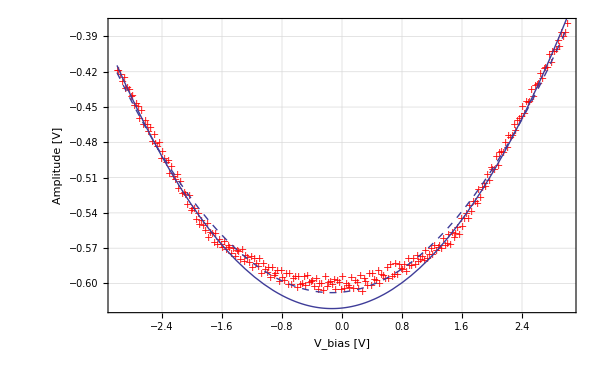

```mathematica
Au18IVBwdEdge=Drop[Au18IVBwd,{Position[Au18IVBwd,-1.5411764383316][[1,1]],
Position[Au18IVBwd,1.5411764383316][[1,1]]}];
ListPlot[Au18IVBwdEdge];
FitU0Au18Bwd=NonlinearModelFit[Au18IVBwdEdge,a(x-V0)^2+b,{a,b,V0},x];
FitU0Au18Bwd2=NonlinearModelFit[Au18IVBwd,a(x-V0)^2+b,{a,b,V0},x];
FitU0Au18Bwd["ParameterTable"]
FitU0Au18Bwd2["ParameterTable"]
Show[ListPlot[Au18IVBwd,PlotMarkers->{"+"},PlotStyle->Red],Plot[Normal[FitU0Au18Bwd],{x,-3,3},PlotStyle->Thick],Plot[Normal[FitU0Au18Bwd2],{x,-3,3},PlotStyle->{Thick,Dashed}],niceStyle,AxesOrigin->{-3,-.8}]
```

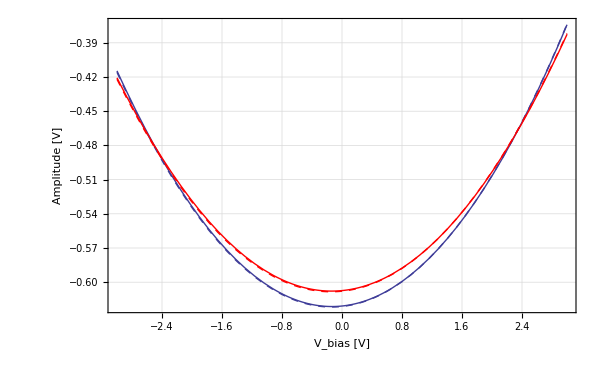

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0251697 | 0.000190925 | 131.831 | 1.46337×10^-132
b | -0.621748 | 0.00108905 | -570.907 | 2.06113×10^-209
V0 | -0.139716 | 0.00332511 | -42.0186 | 5.06111×10^-74

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0228869 | 0.000144262 | 158.648 | 2.7364×10^-255
b | -0.608378 | 0.00058382 | -1042.06 | 1.42800357367137×10^-461
V0 | -0.146103 | 0.00498724 | -29.2954 | 2.86083×10^-83

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.025169 | 0.000204232 | 123.238 | 4.80242×10^-129
b | -0.621341 | 0.00116524 | -533.231 | 7.9485×10^-206
V0 | -0.134066 | 0.00354262 | -37.8437 | 6.56448×10^-69

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0228566 | 0.00015016 | 152.215 | 8.67667×10^-251
b | -0.6078 | 0.000607826 | -999.957 | 4.84805865718675×10^-457
V0 | -0.138838 | 0.00518941 | -26.7541 | 1.0054×10^-75

```mathematica
Show[Plot[Normal[FitU0Au18Bwd],{x,-3,3},PlotRange->All],Plot[Normal[FitU0Au18Fwd],{x,-3,3},PlotStyle->Dashed],
Plot[Normal[FitU0Au18Bwd2],{x,-3,3},PlotStyle->Red],Plot[Normal[FitU0Au18Fwd2],{x,-3,3},PlotStyle->{Red,Dashed}],niceStyle,AxesOrigin->{-3,-.61}]
FitU0Au18Fwd["ParameterTable"]
FitU0Au18Fwd2["ParameterTable"]
FitU0Au18Bwd["ParameterTable"]
FitU0Au18Bwd2["ParameterTable"]
```

### Graphite

#### Graphite 1: C_0022

```mathematica
ListPlot[{C22IVFwd,C22IVBwd}];
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0265481 | 0.000220234 | 120.545 | 6.80815×10^-128
b | -0.605761 | 0.00125756 | -481.693 | 1.73506×10^-200
V0 | -0.112613 | 0.00357112 | -31.5345 | 3.33097×10^-60

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0257971 | 0.000149417 | 172.652 | 1.68912×10^-264
b | -0.602095 | 0.000605296 | -994.713 | 1.83321329005036×10^-456
V0 | -0.109965 | 0.00454872 | -24.1748 | 1.04614×10^-67

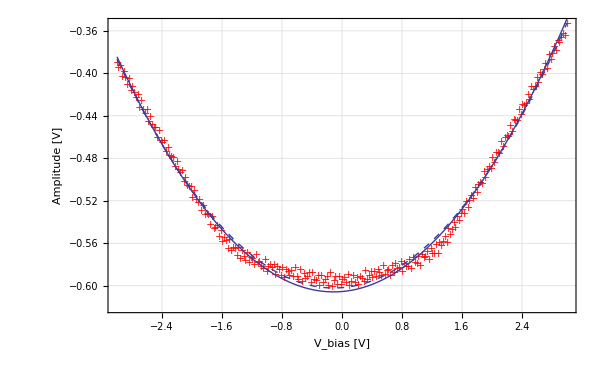

```mathematica
C22IVFwdEdge=Drop[C22IVFwd,{Position[C22IVFwd,-1.5411764383316][[1,1]],
Position[C22IVFwd,1.5411764383316][[1,1]]}];
ListPlot[C22IVFwd];
ListPlot[C22IVFwdEdge];
FitU0C22IVFwd=NonlinearModelFit[C22IVFwdEdge,a(x-V0)^2+b,{a,b,V0},x];
FitU0C22IVFwd2=NonlinearModelFit[C22IVFwd,a(x-V0)^2+b,{a,b,V0},x];
FitU0C22IVFwd["ParameterTable"]
FitU0C22IVFwd2["ParameterTable"]
Show[ListPlot[C22IVFwd,PlotMarkers->{"+"},PlotStyle->Red],Plot[Normal[FitU0C22IVFwd],{x,-3,3},PlotStyle->Thick],Plot[Normal[FitU0C22IVFwd2],{x,-3,3},PlotStyle->{Thick, Dashed}],niceStyle,AxesOrigin->{-3,-0.7}]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0265815 | 0.000236195 | 112.54 | 2.58346×10^-124
b | -0.605544 | 0.00134919 | -448.822 | 8.94532×10^-197
V0 | -0.101826 | 0.00380118 | -26.7881 | 1.06251×10^-52

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.025944 | 0.000147604 | 175.767 | 1.90126×10^-266
b | -0.602517 | 0.000598114 | -1007.36 | 7.49919848611602×10^-458
V0 | -0.0982774 | 0.00445928 | -22.0388 | 8.37372×10^-61

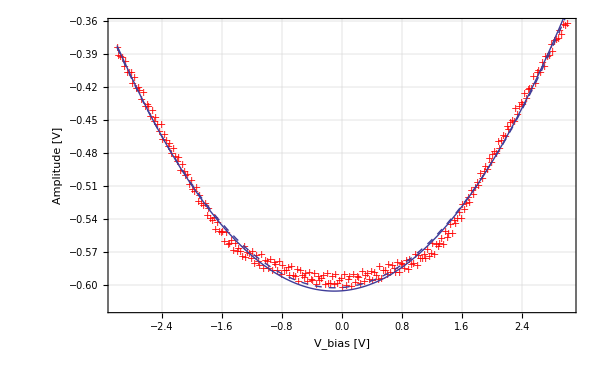

```mathematica
C22IVBwdEdge=Drop[C22IVBwd,{Position[C22IVBwd,-1.5411764383316][[1,1]],
Position[C22IVBwd,1.5411764383316][[1,1]]}];
ListPlot[C22IVBwd];
ListPlot[C22IVBwdEdge];
FitU0C22IVBwd=NonlinearModelFit[C22IVBwdEdge,a(x-V0)^2+b,{a,b,V0},x];
FitU0C22IVBwd2=NonlinearModelFit[C22IVBwd,a(x-V0)^2+b,{a,b,V0},x];
FitU0C22IVBwd["ParameterTable"]
FitU0C22IVBwd2["ParameterTable"]
Show[ListPlot[C22IVBwd,PlotMarkers->{"+"},PlotStyle->Red],Plot[Normal[FitU0C22IVBwd],{x,-3,3},PlotStyle->Thick],Plot[Normal[FitU0C22IVBwd2],{x,-3,3},PlotStyle->{Thick, Dashed}],niceStyle,AxesOrigin->{-3,-0.7}]
```

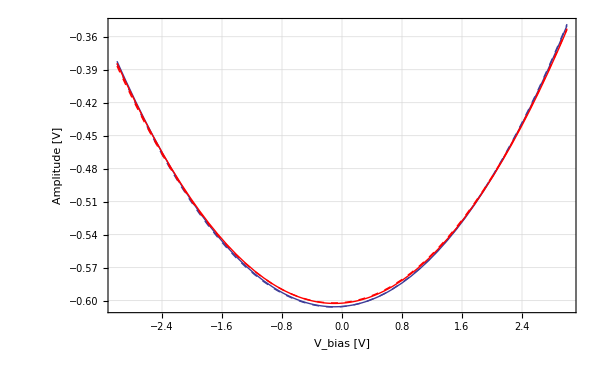

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0265481 | 0.000220234 | 120.545 | 6.80815×10^-128
b | -0.605761 | 0.00125756 | -481.693 | 1.73506×10^-200
V0 | -0.112613 | 0.00357112 | -31.5345 | 3.33097×10^-60

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0257971 | 0.000149417 | 172.652 | 1.68912×10^-264
b | -0.602095 | 0.000605296 | -994.713 | 1.83321329005036×10^-456
V0 | -0.109965 | 0.00454872 | -24.1748 | 1.04614×10^-67

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0265815 | 0.000236195 | 112.54 | 2.58346×10^-124
b | -0.605544 | 0.00134919 | -448.822 | 8.94532×10^-197
V0 | -0.101826 | 0.00380118 | -26.7881 | 1.06251×10^-52

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.025944 | 0.000147604 | 175.767 | 1.90126×10^-266
b | -0.602517 | 0.000598114 | -1007.36 | 7.49919848611602×10^-458
V0 | -0.0982774 | 0.00445928 | -22.0388 | 8.37372×10^-61

```mathematica
Show[Plot[Normal[FitU0C22IVBwd],{x,-3,3},PlotRange->All],Plot[Normal[FitU0C22IVFwd],{x,-3,3},PlotStyle->Dashed],Plot[Normal[FitU0C22IVBwd2],{x,-3,3},PlotRange->All,PlotStyle->Red],Plot[Normal[FitU0C22IVFwd2],{x,-3,3},PlotStyle->{Red,Dashed}],niceStyle,AxesOrigin->{-3,-.61}]
FitU0C22IVFwd["ParameterTable"]
FitU0C22IVFwd2["ParameterTable"]
FitU0C22IVBwd["ParameterTable"]
FitU0C22IVBwd2["ParameterTable"]
```

#### Graphite 2: C_0026

```mathematica
ListPlot[{C26IVFwd,C26IVBwd}];
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0272856 | 0.000232828 | 117.192 | 2.00849×10^-126
b | -0.604251 | 0.00133026 | -454.234 | 2.09909×10^-197
V0 | -0.0940063 | 0.00363498 | -25.8616 | 4.01033×10^-51

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0266972 | 0.000148501 | 179.777 | 6.60735×10^-269
b | -0.601571 | 0.000601856 | -999.526 | 5.40690582884804×10^-457
V0 | -0.0895783 | 0.00435401 | -20.5737 | 6.08879×10^-56

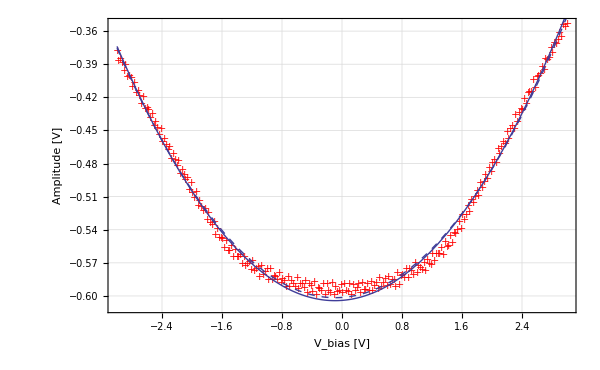

```mathematica
C26IVFwdEdge=Drop[C26IVFwd,{Position[C26IVFwd,-1.5411764383316][[1,1]],
Position[C26IVFwd,1.5411764383316][[1,1]]}];
ListPlot[C26IVFwd];
ListPlot[C26IVFwdEdge];
FitU0C26IVFwd=NonlinearModelFit[C26IVFwdEdge,a(x-V0)^2+b,{a,b,V0},x];
FitU0C26IVFwd2=NonlinearModelFit[C26IVFwd,a(x-V0)^2+b,{a,b,V0},x];
FitU0C26IVFwd["ParameterTable"]
FitU0C26IVFwd2["ParameterTable"]
Show[ListPlot[C26IVFwd,PlotMarkers->{"+"},PlotStyle->Red],Plot[Normal[FitU0C26IVFwd],{x,-3,3},PlotStyle->Thick],Plot[Normal[FitU0C26IVFwd2],{x,-3,3},PlotStyle->{Thick, Dashed}],niceStyle,AxesOrigin->{-3,-.65}]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0273503 | 0.000231749 | 118.016 | 8.66302×10^-127
b | -0.604231 | 0.00132457 | -456.173 | 1.25417×10^-197
V0 | -0.0809849 | 0.00358686 | -22.5782 | 3.31986×10^-45

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0267293 | 0.000146614 | 182.31 | 1.97013×10^-270
b | -0.601377 | 0.000594332 | -1011.85 | 2.43473953456889×10^-458
V0 | -0.0783421 | 0.00428691 | -18.2747 | 3.85771×10^-48

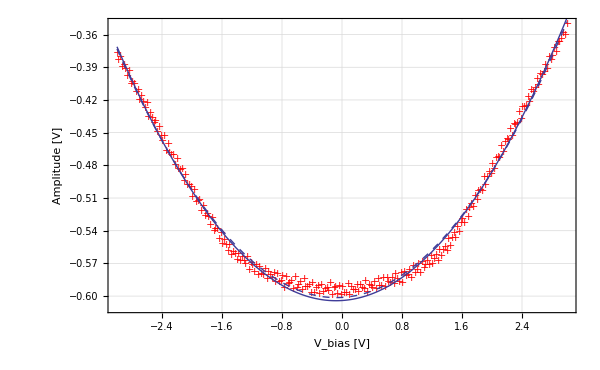

```mathematica
C26IVBwdEdge=Drop[C26IVBwd,{Position[C26IVBwd,-1.5411764383316][[1,1]],
Position[C26IVBwd,1.5411764383316][[1,1]]}];
ListPlot[C26IVBwd];
ListPlot[C26IVBwdEdge];
FitU0C26IVBwd=NonlinearModelFit[C26IVBwdEdge,a(x-V0)^2+b,{a,b,V0},x];
FitU0C26IVBwd2=NonlinearModelFit[C26IVBwd,a(x-V0)^2+b,{a,b,V0},x];
FitU0C26IVBwd["ParameterTable"]
FitU0C26IVBwd2["ParameterTable"]
Show[ListPlot[C26IVBwd,PlotMarkers->{"+"},PlotStyle->Red],Plot[Normal[FitU0C26IVBwd],{x,-3,3},PlotStyle->Thick],Plot[Normal[FitU0C26IVBwd2],{x,-3,3},PlotStyle->{Thick, Dashed}],niceStyle,AxesOrigin->{-3,-.65}]
```

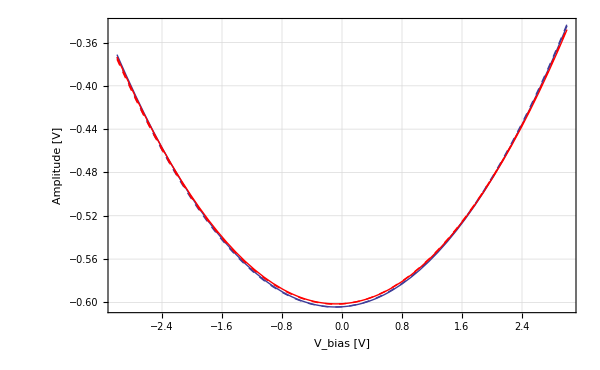

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0272856 | 0.000232828 | 117.192 | 2.00849×10^-126
b | -0.604251 | 0.00133026 | -454.234 | 2.09909×10^-197
V0 | -0.0940063 | 0.00363498 | -25.8616 | 4.01033×10^-51

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0266972 | 0.000148501 | 179.777 | 6.60735×10^-269
b | -0.601571 | 0.000601856 | -999.526 | 5.40690582884804×10^-457
V0 | -0.0895783 | 0.00435401 | -20.5737 | 6.08879×10^-56

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0273503 | 0.000231749 | 118.016 | 8.66302×10^-127
b | -0.604231 | 0.00132457 | -456.173 | 1.25417×10^-197
V0 | -0.0809849 | 0.00358686 | -22.5782 | 3.31986×10^-45

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0267293 | 0.000146614 | 182.31 | 1.97013×10^-270
b | -0.601377 | 0.000594332 | -1011.85 | 2.43473953456889×10^-458
V0 | -0.0783421 | 0.00428691 | -18.2747 | 3.85771×10^-48

```mathematica
Show[Plot[Normal[FitU0C26IVBwd],{x,-3,3},PlotRange->All],Plot[Normal[FitU0C26IVFwd],{x,-3,3},PlotStyle->Dashed],Plot[Normal[FitU0C26IVBwd2],{x,-3,3},PlotRange->All,PlotStyle->Red],Plot[Normal[FitU0C26IVFwd2],{x,-3,3},PlotStyle->{Red,Dashed}],niceStyle,AxesOrigin->{-3,-.61}]
FitU0C26IVFwd["ParameterTable"]
FitU0C26IVFwd2["ParameterTable"]
FitU0C26IVBwd["ParameterTable"]
FitU0C26IVBwd2["ParameterTable"]
```

#### Graphite 3: C_0030

```mathematica
ListPlot[{C30IVFwd,C30IVBwd}];
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0271359 | 0.000226451 | 119.832 | 1.38793×10^-127
b | -0.613378 | 0.00129394 | -474.037 | 1.20454×10^-199
V0 | -0.0908401 | 0.00354918 | -25.5947 | 1.16064×10^-50

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0255308 | 0.000154509 | 165.238 | 1.01844×10^-259
b | -0.60442 | 0.000626202 | -965.217 | 3.71324422454299×10^-453
V0 | -0.089698 | 0.0047372 | -18.9348 | 2.12729×10^-50

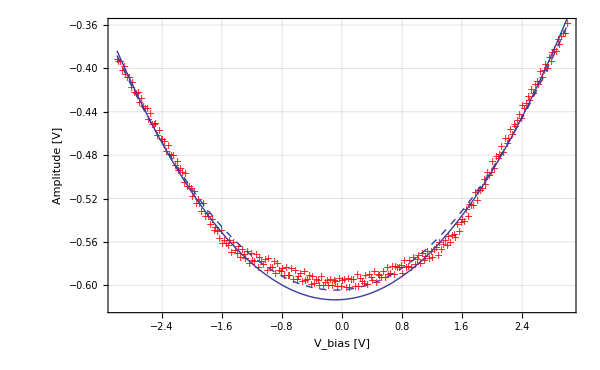

```mathematica
C30IVFwdEdge=Drop[C30IVFwd,{Position[C30IVFwd,-1.5411764383316][[1,1]],
Position[C30IVFwd,1.5411764383316][[1,1]]}];
ListPlot[C30IVFwd];
ListPlot[C30IVFwdEdge];
FitU0C30IVFwd=NonlinearModelFit[C30IVFwdEdge,a(x-V0)^2+b,{a,b,V0},x];
FitU0C30IVFwd2=NonlinearModelFit[C30IVFwd,a(x-V0)^2+b,{a,b,V0},x];
FitU0C30IVFwd["ParameterTable"]
FitU0C30IVFwd2["ParameterTable"]
Show[ListPlot[C30IVFwd,PlotMarkers->{"+"},PlotStyle->Red],Plot[Normal[FitU0C30IVFwd],{x,-3,3},PlotStyle->Thick],Plot[Normal[FitU0C30IVFwd2],{x,-3,3},PlotStyle->{Thick,Dashed}],niceStyle,AxesOrigin->{-3,-0.7}]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0271081 | 0.000229613 | 118.06 | 8.28931×10^-127
b | -0.612887 | 0.00131238 | -467.005 | 7.34124×10^-199
V0 | -0.0804008 | 0.00358459 | -22.4295 | 6.33762×10^-45

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0256361 | 0.000147676 | 173.597 | 4.29793×10^-265
b | -0.604641 | 0.00059864 | -1010.02 | 3.8471235796498×10^-458
V0 | -0.0780625 | 0.00450193 | -17.3398 | 6.37819×10^-45

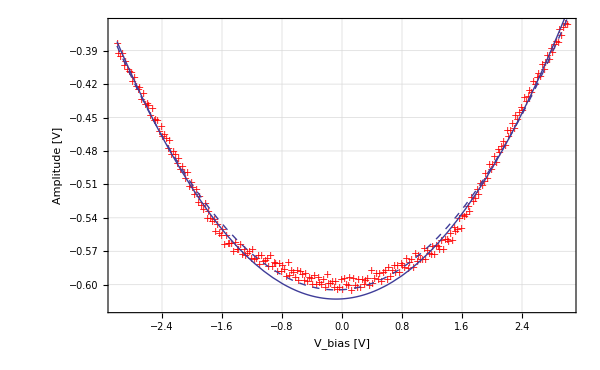

```mathematica
C30IVBwdEdge=Drop[C30IVBwd,{Position[C30IVBwd,-1.5411764383316][[1,1]],
Position[C30IVBwd,1.5411764383316][[1,1]]}];
ListPlot[C30IVBwd];
ListPlot[C30IVBwdEdge];
FitU0C30IVBwd=NonlinearModelFit[C30IVBwdEdge,a(x-V0)^2+b,{a,b,V0},x];
FitU0C30IVBwd2=NonlinearModelFit[C30IVBwd,a(x-V0)^2+b,{a,b,V0},x];
FitU0C30IVBwd["ParameterTable"]
FitU0C30IVBwd2["ParameterTable"]
Show[ListPlot[C30IVBwd,PlotMarkers->{"+"},PlotStyle->Red],Plot[Normal[FitU0C30IVBwd],{x,-3,3},PlotStyle->Thick],Plot[Normal[FitU0C30IVBwd2],{x,-3,3},PlotStyle->{Thick,Dashed}],niceStyle,AxesOrigin->{-3,-0.62}]
```

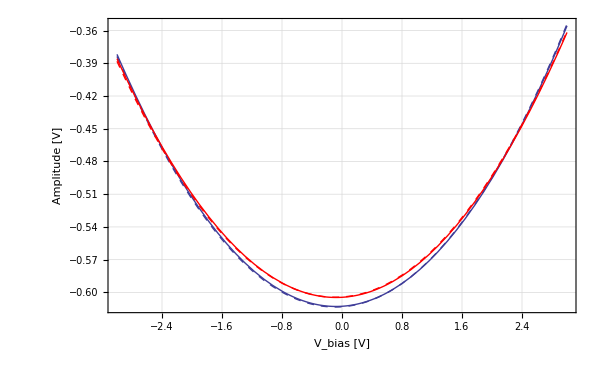

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0272856 | 0.000232828 | 117.192 | 2.00849×10^-126
b | -0.604251 | 0.00133026 | -454.234 | 2.09909×10^-197
V0 | -0.0940063 | 0.00363498 | -25.8616 | 4.01033×10^-51

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0266972 | 0.000148501 | 179.777 | 6.60735×10^-269
b | -0.601571 | 0.000601856 | -999.526 | 5.40690582884804×10^-457
V0 | -0.0895783 | 0.00435401 | -20.5737 | 6.08879×10^-56

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0273503 | 0.000231749 | 118.016 | 8.66302×10^-127
b | -0.604231 | 0.00132457 | -456.173 | 1.25417×10^-197
V0 | -0.0809849 | 0.00358686 | -22.5782 | 3.31986×10^-45

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0267293 | 0.000146614 | 182.31 | 1.97013×10^-270
b | -0.601377 | 0.000594332 | -1011.85 | 2.43473953456889×10^-458
V0 | -0.0783421 | 0.00428691 | -18.2747 | 3.85771×10^-48

```mathematica
Show[Plot[Normal[FitU0C30IVBwd],{x,-3,3},PlotRange->All],Plot[Normal[FitU0C30IVFwd],{x,-3,3},PlotStyle->Dashed],Plot[Normal[FitU0C30IVBwd2],{x,-3,3},PlotRange->All,PlotStyle->Red],Plot[Normal[FitU0C30IVFwd2],{x,-3,3},PlotStyle->{Red,Dashed}],niceStyle,AxesOrigin->{-3,-.61}]
FitU0C26IVFwd["ParameterTable"]
FitU0C26IVFwd2["ParameterTable"]
FitU0C26IVBwd["ParameterTable"]
FitU0C26IVBwd2["ParameterTable"]
```

## Fitting IV-Curves with feedback

### Define Functions for Fitting

```mathematica
(*Z Calibration*)calib:=27.6*10^-9(*27.6*10^-9 m/V; 276 Å/V*)
Zgain:=15(*15*)
```

```mathematica
ϵ0:=8.854187817*10^-12(*vacuum permittivity in As/(V m)*)
Q:=206.356
A0:=1.006(*V*)
A:=0.6(*V*)
agrad:=A0/A
k:=2.01602(*N/(m)*)
```

```mathematica
agrad
```

1.67667

```mathematica
FGrad=k((1-2(agrad)^2+√(4 Q^2((agrad)^2-1)+1))/(2(Q^2-(agrad)^2)))(*N/m*)
```

0.0130395

```mathematica
FitFunctionPlane[R_,U_]=((π ϵ0 R^2)/FGrad)^(1/3)(Abs[U-U0])^(2/3)
```

0.0012873 (R^2)^(1/3) Abs[U-U0]^(2/3)

### Gold on Graphite

#### Gold1 : Au_ 0087

| Estimate | Standard Error | t-Statistic | P-Value
m | 1.5994×10^-9 | 8.12211×10^-12 | 196.919 | 1.27067×10^-155
U0 | -0.418286 | 0.00617122 | -67.7801 | 2.88165×10^-99
c | -2.83293×10^-9 | 5.00441×10^-11 | -56.6087 | 6.06333×10^-90

r→1.19916

0.00761487

| Estimate | Standard Error | t-Statistic | P-Value
α | 1.3814×10^-11 | 7.58409×10^-14 | 182.145 | 1.80314×10^-151
U0 | -0.396434 | 0.0130995 | -30.2632 | 7.8315×10^-59
c | 1.8373×10^-9 | 5.81715×10^-11 | 31.5842 | 7.41039×10^-61

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

x→0.0712854

4.08435

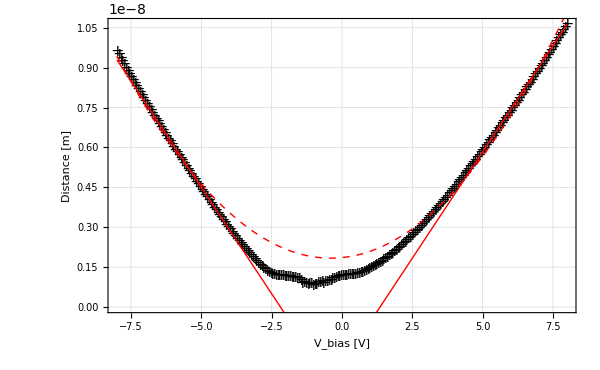

```mathematica
(*Au87IVFwdFit=Drop[Au87IVFwd,{Position[Au87IVFwd,-4.04705905914307][[1,1]],
Position[Au87IVFwd,4.04705905914307][[1,1]]}];*)
Au87IVFwdFitTemp=Drop[Au87IVFwd,{Position[Au87IVFwd,-4.04705905914307][[1,1]],
Position[Au87IVFwd,4.04705905914307][[1,1]]}];
Au87IVFwdFit=Replace[Au87IVFwdFitTemp,{xi_,yi_}->{xi,calib*yi/Zgain},2];
FitSphereAu87Fwd=NonlinearModelFit[Au87IVFwdFit,m Abs[U-U0]+c,{m,U0,c},U];
FitSphereAu87Fwd["ParameterTable"]
NSolve[((Pi ϵ0 r*10^-9)/FGrad)^(1/2)==FitSphereAu87Fwd["ParameterTable"][[1,1,2,2]],r][[1,1]]
(2FGrad)/(Pi ϵ0)FitSphereAu87Fwd["ParameterTable"][[1,1,2,3]]
FitConeAu87Fwd=NonlinearModelFit[Au87IVFwdFit,( α ((U-U0)))^2/(4Pi ϵ0 FGrad)+c,{α,U0,c},U];
FitConeAu87Fwd["ParameterTable"]
NSolve[2Pi ϵ0(ArcSinh[1/Tan[x/2]])^-1==FitConeAu87Fwd["ParameterTable"][[1,1,2,2]],x,WorkingPrecision->Infinity][[1,1]]
(Pi/180)^-1*2*ArcTan[1/Sinh[(2 Pi ϵ0)/θ]]/.θ->FitConeAu87Fwd["ParameterTable"][[1,1,2,2]]
Show[ListPlot[{Replace[Au87IVFwd,{Vi_,ki_}->{Vi,calib*ki/Zgain},2]},PlotStyle->{Black},PlotMarkers->{"+",16}],Plot[Normal[FitSphereAu87Fwd],{U,-8,8},PlotRange->Full,PlotStyle->{Thick,Red}],Plot[Normal[FitConeAu87Fwd],{U,-8,8},PlotStyle->{Thick,Dashed,Red}],ImageSize->600,niceStyle2]
```

| Estimate | Standard Error | t-Statistic | P-Value
m | 1.59962×10^-9 | 5.34132×10^-12 | 299.48 | 5.69779×10^-178
U0 | -0.39651 | 0.00403334 | -98.308 | 9.15672×10^-119
c | -2.84085×10^-9 | 3.29104×10^-11 | -86.3209 | 6.44496×10^-112

r→1.19949

0.00500775

| Estimate | Standard Error | t-Statistic | P-Value
α | 1.3815×10^-11 | 5.44503×10^-14 | 253.718 | 3.97622×10^-169
U0 | -0.382987 | 0.00936948 | -40.876 | 1.96147×10^-73
c | 1.83137×10^-9 | 4.1777×10^-11 | 43.8368 | 6.2415×10^-77

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

x→0.0713065

4.08556

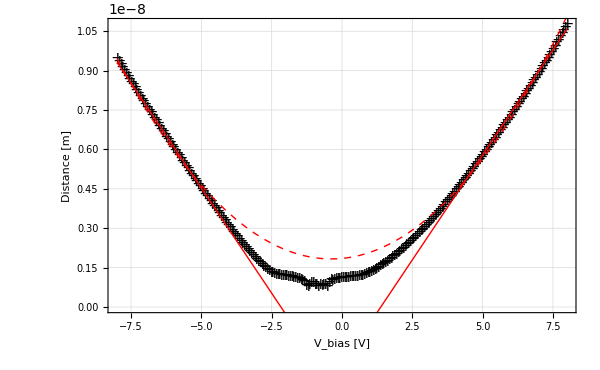

```mathematica
(*Au87IVBwdFit=Drop[Au87IVBwd,{Position[Au87IVBwd,-4.04705905914307][[1,1]],
Position[Au87IVBwd,4.04705905914307][[1,1]]}];*)
Au87IVBwdFitTemp=Drop[Au87IVBwd,{Position[Au87IVBwd,-4.04705905914307][[1,1]],
Position[Au87IVBwd,4.04705905914307][[1,1]]}];
Au87IVBwdFit=Replace[Au87IVBwdFitTemp,{xi_,yi_}->{xi,calib*yi/Zgain},2];
FitSphereAu87Bwd=NonlinearModelFit[Au87IVBwdFit,m Abs[U-U0]+c,{m,U0,c},U];
FitSphereAu87Bwd["ParameterTable"]
NSolve[((Pi ϵ0 r*10^-9)/FGrad)^(1/2)==FitSphereAu87Bwd["ParameterTable"][[1,1,2,2]],r][[1,1]]
(2FGrad)/(Pi ϵ0)FitSphereAu87Bwd["ParameterTable"][[1,1,2,3]]
FitConeAu87Bwd=NonlinearModelFit[Au87IVBwdFit,( α ((U-U0)))^2/(4Pi ϵ0 FGrad)+c,{α,U0,c},U];
FitConeAu87Bwd["ParameterTable"]
NSolve[2Pi ϵ0(ArcSinh[1/Tan[x/2]])^-1==FitConeAu87Bwd["ParameterTable"][[1,1,2,2]],x,WorkingPrecision->Infinity][[1,1]]
(Pi/180)^-1*2*ArcTan[1/Sinh[(2 Pi ϵ0)/θ]]/.θ->FitConeAu87Bwd["ParameterTable"][[1,1,2,2]]
Show[ListPlot[{Replace[Au87IVBwd,{Vi_,ki_}->{Vi,calib*ki/Zgain},2]},PlotStyle->{Black},PlotMarkers->{"+",16}],Plot[Normal[FitSphereAu87Bwd],{U,-8,8},PlotRange->Full,PlotStyle->{Thick,Red}],Plot[Normal[FitConeAu87Bwd],{U,-8,8},PlotStyle->{Thick,Dashed,Red}],ImageSize->600,niceStyle2]
```

#### Gold2 : Au_ 0097

| Estimate | Standard Error | t-Statistic | P-Value
R | 1.6363×10^-9 | 8.1091×10^-12 | 201.786 | 6.36415×10^-157
U0 | -0.349415 | 0.00591357 | -59.087 | 3.75325×10^-92
c | -3.38561×10^-9 | 4.99639×10^-11 | -67.7611 | 2.98043×10^-99

r→1.25514

0.00760267

| Estimate | Standard Error | t-Statistic | P-Value
α | 1.39773×10^-11 | 6.20805×10^-14 | 225.148 | 9.27641×10^-163
U0 | -0.331734 | 0.0104206 | -31.8344 | 3.11765×10^-61
c | 1.39518×10^-9 | 4.82292×10^-11 | 28.9281 | 1.02216×10^-56

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

x→0.074719

4.28108

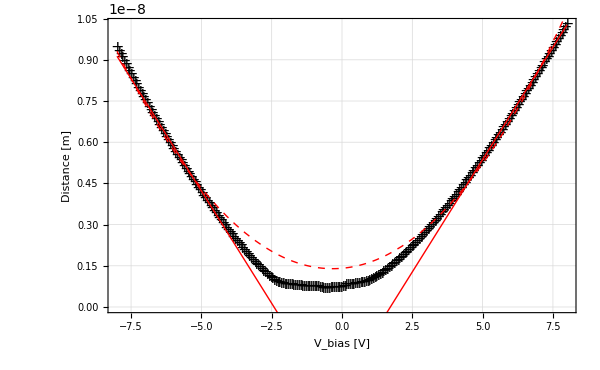

```mathematica
Au97IVFwdFitTemp=Drop[Au97IVFwd,{Position[Au97IVFwd,-4.04705905914307][[1,1]],
Position[Au97IVFwd,4.04705905914307][[1,1]]}];
Au97IVFwdFit=Replace[Au97IVFwdFitTemp,{xi_,yi_}->{xi,calib*yi/Zgain},2];
FitSphereAu97Fwd=NonlinearModelFit[Au97IVFwdFit,R Abs[U-U0]+c,{R,U0,c},U];
FitSphereAu97Fwd["ParameterTable"]
NSolve[((Pi ϵ0 r*10^-9)/FGrad)^(1/2)==FitSphereAu97Fwd["ParameterTable"][[1,1,2,2]],r][[1,1]]
(2FGrad)/(Pi ϵ0)FitSphereAu97Fwd["ParameterTable"][[1,1,2,3]]
FitConeAu97Fwd=NonlinearModelFit[Au97IVFwdFit,( α (U-U0))^2/(4Pi ϵ0 FGrad)+c,{α,U0,c},U];
FitConeAu97Fwd["ParameterTable"]
NSolve[2Pi ϵ0(ArcSinh[1/Tan[x/2]])^-1==FitConeAu97Fwd["ParameterTable"][[1,1,2,2]],x,WorkingPrecision->Infinity][[1,1]]
(180/Pi)2*ArcTan[1/Sinh[(2 Pi ϵ0)/α]]/.α->FitConeAu97Fwd["ParameterTable"][[1,1,2,2]]
Show[ListPlot[{Replace[Au97IVFwd,{Vi_,ki_}->{Vi,calib*ki/Zgain},2]},PlotStyle->{Black},PlotMarkers->{"+",16}],Plot[Normal[FitSphereAu97Fwd],{U,-8,8},PlotRange->Full,PlotStyle->{Thick,Red}],Plot[Normal[FitConeAu97Fwd],{U,-8,8},PlotStyle->{Thick,Dashed,Red}],ImageSize->600,niceStyle2]
```

| Estimate | Standard Error | t-Statistic | P-Value
R | 1.63578×10^-9 | 6.22809×10^-12 | 262.645 | 5.69598×10^-171
U0 | -0.32605 | 0.00451805 | -72.1661 | 1.55521×10^-102
c | -3.38708×10^-9 | 3.83742×10^-11 | -88.2645 | 4.35056×10^-113

r→1.25434

0.00583914

| Estimate | Standard Error | t-Statistic | P-Value
α | 1.39745×10^-11 | 4.10698×10^-14 | 340.262 | 8.79157×10^-185
U0 | -0.316653 | 0.00687069 | -46.0876 | 1.87456×10^-79
c | 1.39392×10^-9 | 3.19068×10^-11 | 43.6874 | 9.26319×10^-77

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

x→0.0746593

4.27766

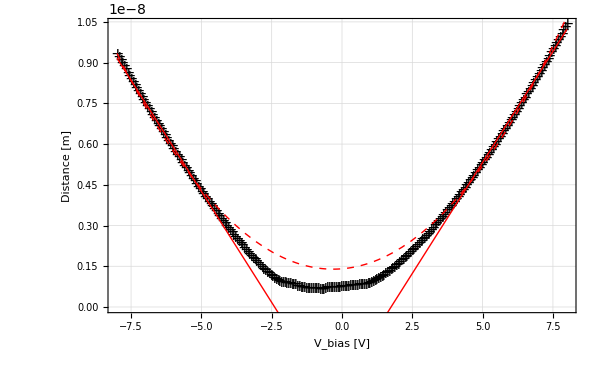

```mathematica
Au97IVBwdFitTemp=Drop[Au97IVBwd,{Position[Au97IVBwd,-4.04705905914307][[1,1]],
Position[Au97IVBwd,4.04705905914307][[1,1]]}];
Au97IVBwdFit=Replace[Au97IVBwdFitTemp,{xi_,yi_}->{xi,calib*yi/Zgain},2];
FitSphereAu97Bwd=NonlinearModelFit[Au97IVBwdFit,R Abs[U-U0]+c,{R,U0,c},U];
FitSphereAu97Bwd["ParameterTable"]
NSolve[((Pi ϵ0 r*10^-9)/FGrad)^(1/2)==FitSphereAu97Bwd["ParameterTable"][[1,1,2,2]],r][[1,1]]
(2FGrad)/(Pi ϵ0)FitSphereAu97Bwd["ParameterTable"][[1,1,2,3]]
FitConeAu97Bwd=NonlinearModelFit[Au97IVBwdFit,( α (U-U0))^2/(4Pi ϵ0 FGrad)+c,{α,U0,c},U];
FitConeAu97Bwd["ParameterTable"]
NSolve[2Pi ϵ0(ArcSinh[1/Tan[x/2]])^-1==FitConeAu97Bwd["ParameterTable"][[1,1,2,2]],x,WorkingPrecision->Infinity][[1,1]]
(180/Pi)*2*ArcTan[1/Sinh[(2 Pi ϵ0)/α]]/.α->FitConeAu97Bwd["ParameterTable"][[1,1,2,2]]
Show[ListPlot[Replace[Au97IVBwd,{xi_,yi_}->{xi,calib*yi/Zgain},2],PlotStyle->{Black},PlotMarkers->{"+",16}],Plot[Normal[FitSphereAu97Bwd],{U,-8,8},PlotRange->Full,PlotStyle->{Thick,Red}],Plot[Normal[FitConeAu97Bwd],{U,-8,8},PlotStyle->{Thick,Dashed,Red}],ImageSize->600,niceStyle2]
```

#### Gold3 : Au_ 0107

| Estimate | Standard Error | t-Statistic | P-Value
R | 1.68606×10^-9 | 7.99439×10^-12 | 210.906 | 2.81367×10^-159
U0 | -0.34359 | 0.00564984 | -60.8141 | 1.2186×10^-93
c | -3.74606×10^-9 | 4.92572×10^-11 | -76.051 | 2.83027×10^-105

r→1.33263

0.00749513

| Estimate | Standard Error | t-Statistic | P-Value
α | 1.41858×10^-11 | 6.43091×10^-14 | 220.588 | 1.14233×10^-161
U0 | -0.325943 | 0.0106213 | -30.6876 | 1.72268×10^-59
c | 1.18246×10^-9 | 5.071×10^-11 | 23.3181 | 5.69874×10^-47

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

x→0.0792191

4.53892

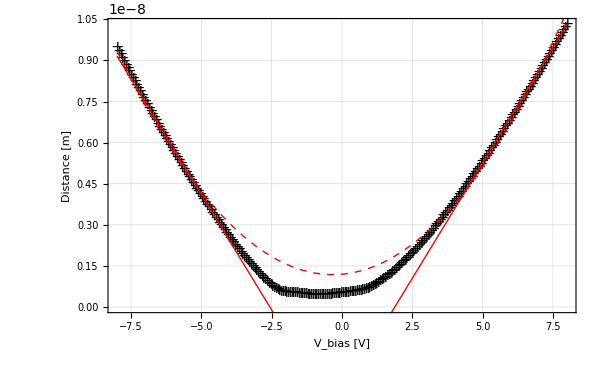

```mathematica
Au107IVFwdFitTemp=Drop[Au107IVFwd,{Position[Au107IVFwd,-4.04705905914307][[1,1]],
Position[Au107IVFwd,4.04705905914307][[1,1]]}];
Au107IVFwdFit=Replace[Au107IVFwdFitTemp,{xi_,yi_}->{xi,calib*yi/Zgain},2];
FitSphereAu107Fwd=NonlinearModelFit[Au107IVFwdFit,R Abs[U-U0]+c,{R,U0,c},U];
FitSphereAu107Fwd["ParameterTable"]
NSolve[((Pi ϵ0 r*10^-9)/FGrad)^(1/2)==FitSphereAu107Fwd["ParameterTable"][[1,1,2,2]],r][[1,1]]
(2 FGrad)/(Pi ϵ0)FitSphereAu107Fwd["ParameterTable"][[1,1,2,3]]
FitConeAu107Fwd=NonlinearModelFit[Au107IVFwdFit,( α (U-U0))^2/(4Pi ϵ0 FGrad)+c,{α,U0,c},U];
FitConeAu107Fwd["ParameterTable"]
NSolve[2Pi ϵ0(ArcSinh[1/Tan[x/2]])^-1==FitConeAu107Fwd["ParameterTable"][[1,1,2,2]],x,WorkingPrecision->Infinity][[1,1]]
(180/Pi)*2*ArcTan[1/Sinh[(2 Pi ϵ0)/α]]/.α->FitConeAu107Fwd["ParameterTable"][[1,1,2,2]]
Show[ListPlot[Replace[Au107IVFwd,{xi_,yi_}->{xi,calib*yi/Zgain},2],PlotStyle->{Black},PlotMarkers->{"+",16}],Plot[Normal[FitSphereAu107Fwd],{U,-8,8},PlotRange->Full,PlotStyle->{Thick,Red}],Plot[Normal[FitConeAu107Fwd],{U,-8,8},PlotStyle->{Thick,Dashed,Red}],ImageSize->600,niceStyle2]
```

| Estimate | Standard Error | t-Statistic | P-Value
R | 1.68572×10^-9 | 5.7368×10^-12 | 293.843 | 5.87976×10^-177
U0 | -0.327744 | 0.00403995 | -81.1257 | 1.17003×10^-108
c | -3.74595×10^-9 | 3.53471×10^-11 | -105.976 | 9.90801×10^-123

r→1.33209

0.00537853

| Estimate | Standard Error | t-Statistic | P-Value
α | 1.41835×10^-11 | 4.40891×10^-14 | 321.702 | 8.65084×10^-182
U0 | -0.318258 | 0.0072698 | -43.7781 | 7.28793×10^-77
c | 1.18285×10^-9 | 3.47641×10^-11 | 34.0251 | 1.98915×10^-64

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

x→0.0791695

4.53608

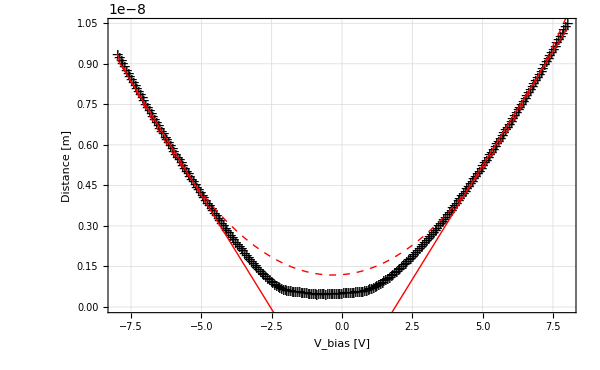

```mathematica
Au107IVBwdFitTemp=Drop[Au107IVBwd,{Position[Au107IVBwd,-4.04705905914307][[1,1]],
Position[Au107IVBwd,4.04705905914307][[1,1]]}];
Au107IVBwdFit=Replace[Au107IVBwdFitTemp,{xi_,yi_}->{xi,calib*yi/Zgain},2];
FitSphereAu107Bwd=NonlinearModelFit[Au107IVBwdFit,R Abs[U-U0]+c,{R,U0,c},U];
FitSphereAu107Bwd["ParameterTable"]
NSolve[((Pi ϵ0 r*10^-9)/FGrad)^(1/2)==FitSphereAu107Bwd["ParameterTable"][[1,1,2,2]],r][[1,1]]
(2 FGrad)/(Pi ϵ0)FitSphereAu107Bwd["ParameterTable"][[1,1,2,3]]
FitConeAu107Bwd=NonlinearModelFit[Au107IVBwdFit,( α (U-U0))^2/(4Pi ϵ0 FGrad)+c,{α,U0,c},U];
FitConeAu107Bwd["ParameterTable"]
NSolve[2Pi ϵ0(ArcSinh[1/Tan[x/2]])^-1==FitConeAu107Bwd["ParameterTable"][[1,1,2,2]],x,WorkingPrecision->Infinity][[1,1]]
(180/Pi)*2*ArcTan[1/Sinh[(2 Pi ϵ0)/α]]/.α->FitConeAu107Bwd["ParameterTable"][[1,1,2,2]]
Show[ListPlot[Replace[Au107IVBwd,{xi_,yi_}->{xi,calib*yi/Zgain},2],PlotStyle->{Black},PlotMarkers->{"+",16}],Plot[Normal[FitSphereAu107Bwd],{U,-8,8},PlotRange->Full,PlotStyle->{Thick,Red}],Plot[Normal[FitConeAu107Bwd],{U,-8,8},PlotStyle->{Thick,Dashed,Red}],ImageSize->600,niceStyle2]
```

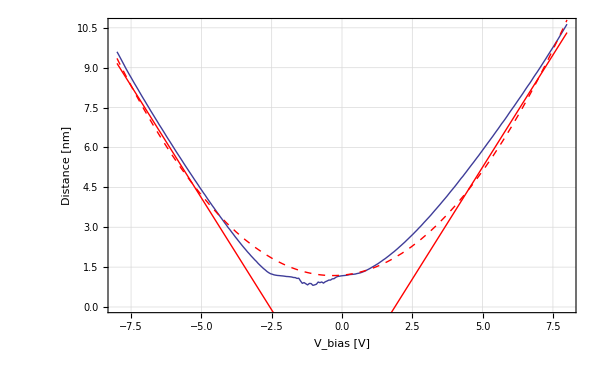

```mathematica
FitSphereAu87Fwd2=NonlinearModelFit[Replace[Au107IVFwdFitTemp,{xi_,yi_}->{xi,calib*yi/15*10^9},2],m Abs[U-U0]+c,{m,U0,c},U];
FitConeAu87Fwd2=NonlinearModelFit[Replace[Au107IVFwdFitTemp,{xi_,yi_}->{xi,calib*yi/15*10^9},2],( α ((U-U0)))^2/(4Pi ϵ0 FGrad)+c,{α,U0,c},U];
Show[ListLinePlot[{Replace[Au87IVFwd,{Vi_,ki_}->{Vi,calib*ki/15*10^9},2]},PlotStyle->{Thick}],Plot[Normal[FitSphereAu87Fwd2],{U,-8,8},PlotRange->Full,PlotStyle->{Thick,Red}],Plot[Normal[FitConeAu87Fwd2],{U,-8,8},PlotStyle->{Thick,Dashed,Red}],ImageSize->600,
Axes->True,
Frame->True,
GridLines->Automatic,
ImageSize->600,
ImageMargins->3,
LabelStyle->{"Arial",16,Bold},
BaseStyle->{FontFamily->"Arial",FontSize->16},
FrameTicksStyle->{Directive[16,Plain],Directive[16,Plain]},
FrameStyle->Thick,
GridLinesStyle->Directive[Dashed,Gray],
AxesStyle->Directive[Thick,Dashed],
FrameLabel->{"V_bias [V]","Distance [nm]"}]
```

### Graphite

#### Graphite1 : C_ 0057

FittedModel[-4.95451×10^-9+1.70357×10^-9 Abs[0.231649+U]]

| Estimate | Standard Error | t-Statistic | P-Value
m | 1.70357×10^-9 | 7.93993×10^-12 | 214.557 | 3.42551×10^-160
U0 | -0.231649 | 0.00542629 | -42.6902 | 1.33183×10^-75
c | -4.95451×10^-9 | 4.89216×10^-11 | -101.274 | 2.47129×10^-120

r→1.36046

0.00744407

| Estimate | Standard Error | t-Statistic | P-Value
α | 1.42634×10^-11 | 4.58598×10^-14 | 311.021 | 5.47523×10^-180
U0 | -0.219772 | 0.0073723 | -29.8105 | 4.01079×10^-58
c | 3.02308×10^-11 | 3.64057×10^-11 | 0.830386 | 0.407929

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

x→0.0809266

4.63675

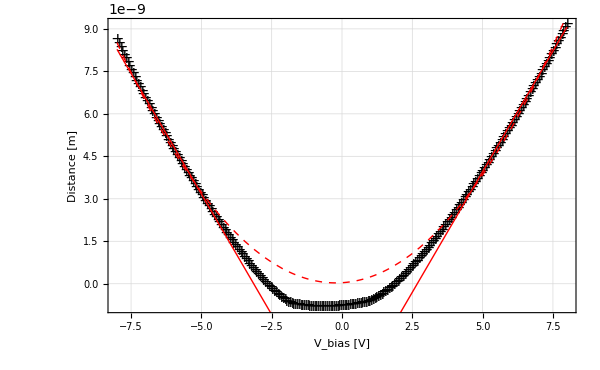

```mathematica
C57IVFwdFitTemp=Drop[C57IVFwd,{Position[C57IVFwd,-4.04705905914307][[1,1]],
Position[C57IVFwd,4.04705905914307][[1,1]]}];
C57IVFwdFit=Replace[C57IVFwdFitTemp,{xi_,yi_}->{xi,calib*yi/Zgain},2];
FitSphereC57Fwd=NonlinearModelFit[C57IVFwdFit,m Abs[U-U0]+c,{m,U0,c},U]
FitSphereC57Fwd["ParameterTable"]
NSolve[((Pi ϵ0 r*10^-9)/FGrad)^(1/2)==FitSphereC57Fwd["ParameterTable"][[1,1,2,2]],r][[1,1]]
(2FGrad)/(Pi ϵ0)FitSphereC57Fwd["ParameterTable"][[1,1,2,3]]
FitConeC57Fwd=NonlinearModelFit[C57IVFwdFit,( α ((U-U0)))^2/(4Pi ϵ0 FGrad)+c,{α,U0,c},U];
FitConeC57Fwd["ParameterTable"]
NSolve[2Pi ϵ0(ArcSinh[1/Tan[x/2]])^-1==FitConeC57Fwd["ParameterTable"][[1,1,2,2]],x,WorkingPrecision->Infinity][[1,1]]
(Pi/180)^-1*2*ArcTan[1/Sinh[(2 Pi ϵ0)/θ]]/.θ->FitConeC57Fwd["ParameterTable"][[1,1,2,2]]
Show[ListPlot[{Replace[C57IVFwd,{Vi_,ki_}->{Vi,calib*ki/Zgain},2]},PlotStyle->{Black},PlotMarkers->{"+",16}],Plot[Normal[FitSphereC57Fwd],{U,-8,8},PlotRange->Full,PlotStyle->{Thick,Red}],Plot[Normal[FitConeC57Fwd],{U,-8,8},PlotStyle->{Thick,Dashed,Red}],ImageSize->600,niceStyle2]
```

| Estimate | Standard Error | t-Statistic | P-Value
m | 1.70278×10^-9 | 7.41824×10^-12 | 229.54 | 8.66803×10^-164
U0 | -0.21313 | 0.00505667 | -42.1484 | 5.8×10^-75
c | -4.9593×10^-9 | 4.57072×10^-11 | -108.501 | 5.6405×10^-124

r→1.3592

0.00695496

| Estimate | Standard Error | t-Statistic | P-Value
α | 1.42594×10^-11 | 2.81285×10^-14 | 506.938 | 4.60358×10^-206
U0 | -0.210054 | 0.00451593 | -46.5139 | 6.41968×10^-80
c | 2.42063×10^-11 | 2.23256×10^-11 | 1.08424 | 0.280378

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

x→0.0808391

4.63174

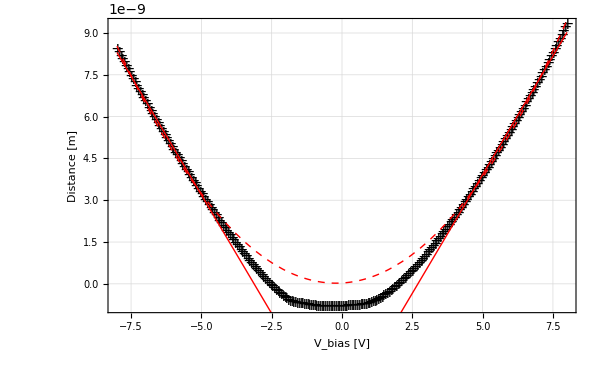

```mathematica
C57IVBwdFitTemp=Drop[C57IVBwd,{Position[C57IVBwd,-4.04705905914307][[1,1]],
Position[C57IVBwd,4.04705905914307][[1,1]]}];
C57IVBwdFit=Replace[C57IVBwdFitTemp,{xi_,yi_}->{xi,calib*yi/Zgain},2];
FitSphereC57Bwd=NonlinearModelFit[C57IVBwdFit,m Abs[U-U0]+c,{m,U0,c},U];
FitSphereC57Bwd["ParameterTable"]
NSolve[((Pi ϵ0 r*10^-9)/FGrad)^(1/2)==FitSphereC57Bwd["ParameterTable"][[1,1,2,2]],r][[1,1]]
(2FGrad)/(Pi ϵ0)FitSphereC57Bwd["ParameterTable"][[1,1,2,3]]
FitConeC57Bwd=NonlinearModelFit[C57IVBwdFit,( α ((U-U0)))^2/(4Pi ϵ0 FGrad)+c,{α,U0,c},U];
FitConeC57Bwd["ParameterTable"]
NSolve[2Pi ϵ0(ArcSinh[1/Tan[x/2]])^-1==FitConeC57Bwd["ParameterTable"][[1,1,2,2]],x,WorkingPrecision->Infinity][[1,1]]
(Pi/180)^-1*2*ArcTan[1/Sinh[(2 Pi ϵ0)/θ]]/.θ->FitConeC57Bwd["ParameterTable"][[1,1,2,2]]
Show[ListPlot[{Replace[C57IVBwd,{Vi_,ki_}->{Vi,calib*ki/Zgain},2]},PlotStyle->{Black},PlotMarkers->{"+",16}],Plot[Normal[FitSphereC57Bwd],{U,-8,8},PlotRange->Full,PlotStyle->{Thick,Red}],Plot[Normal[FitConeC57Bwd],{U,-8,8},PlotStyle->{Thick,Dashed,Red}],ImageSize->600,niceStyle2]
```

#### Graphite2 : C_ 0067

| Estimate | Standard Error | t-Statistic | P-Value
m | 1.76111×10^-9 | 8.55231×10^-12 | 205.923 | 5.28391×10^-158
U0 | -0.255402 | 0.0056779 | -44.9817 | 3.14964×10^-78
c | -4.62091×10^-9 | 5.26948×10^-11 | -87.692 | 9.56636×10^-113

r→1.36046

0.00744407

| Estimate | Standard Error | t-Statistic | P-Value
α | 1.44998×10^-11 | 5.56246×10^-14 | 260.673 | 1.43705×10^-170
U0 | -0.240834 | 0.00882864 | -27.2787 | 5.31824×10^-54
c | 5.32649×10^-10 | 4.488×10^-11 | 11.8683 | 4.02228×10^-22

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

x→0.0862396

4.94116

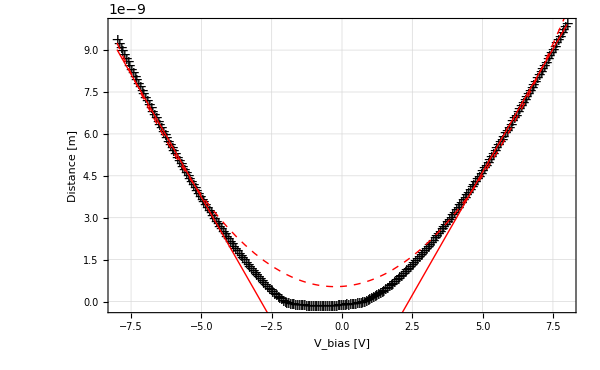

```mathematica
C67IVFwdFitTemp=Drop[C67IVFwd,{Position[C67IVFwd,-4.04705905914307][[1,1]],
Position[C67IVFwd,4.04705905914307][[1,1]]}];
C67IVFwdFit=Replace[C67IVFwdFitTemp,{xi_,yi_}->{xi,calib*yi/Zgain},2];
FitSphereC67Fwd=NonlinearModelFit[C67IVFwdFit,m Abs[U-U0]+c,{m,U0,c},U];
FitSphereC67Fwd["ParameterTable"]
NSolve[((Pi ϵ0 r*10^-9)/FGrad)^(1/2)==FitSphereC57Fwd["ParameterTable"][[1,1,2,2]],r][[1,1]]
(2FGrad)/(Pi ϵ0)FitSphereC57Fwd["ParameterTable"][[1,1,2,3]]
FitConeC67Fwd=NonlinearModelFit[C67IVFwdFit,( α ((U-U0)))^2/(4Pi ϵ0 FGrad)+c,{α,U0,c},U];
FitConeC67Fwd["ParameterTable"]
NSolve[2Pi ϵ0(ArcSinh[1/Tan[x/2]])^-1==FitConeC67Fwd["ParameterTable"][[1,1,2,2]],x,WorkingPrecision->Infinity][[1,1]]
(Pi/180)^-1*2*ArcTan[1/Sinh[(2 Pi ϵ0)/θ]]/.θ->FitConeC67Fwd["ParameterTable"][[1,1,2,2]]
Show[ListPlot[{Replace[C67IVFwd,{Vi_,ki_}->{Vi,calib*ki/Zgain},2]},PlotStyle->{Black},PlotMarkers->{"+",16}],Plot[Normal[FitSphereC67Fwd],{U,-8,8},PlotRange->Full,PlotStyle->{Thick,Red}],Plot[Normal[FitConeC67Fwd],{U,-8,8},PlotStyle->{Thick,Dashed,Red}],ImageSize->600,niceStyle2]
```

| Estimate | Standard Error | t-Statistic | P-Value
m | 1.75873×10^-9 | 6.54401×10^-12 | 268.754 | 3.38548×10^-172
U0 | -0.243621 | 0.00434112 | -56.1194 | 1.69541×10^-89
c | -4.61061×10^-9 | 4.03207×10^-11 | -114.349 | 9.43625×10^-127

r→1.44997

0.00613532

| Estimate | Standard Error | t-Statistic | P-Value
α | 1.44889×10^-11 | 3.52583×10^-14 | 410.936 | 7.44333×10^-195
U0 | -0.238025 | 0.00559752 | -42.5232 | 2.09209×10^-75
c | 5.37003×10^-10 | 2.8427×10^-11 | 18.8906 | 3.63185×10^-38

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

x→0.0859897

4.92685

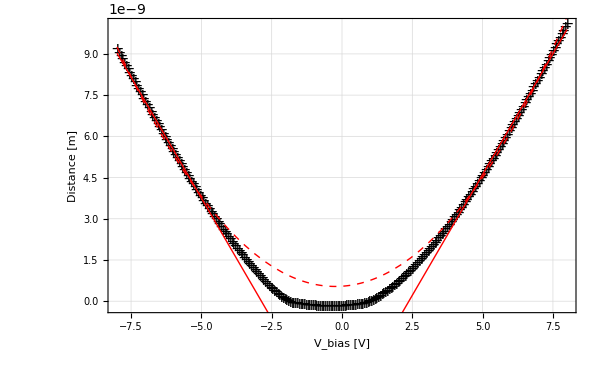

```mathematica
C67IVBwdFitTemp=Drop[C67IVBwd,{Position[C67IVBwd,-4.04705905914307][[1,1]],
Position[C67IVBwd,4.04705905914307][[1,1]]}];
C67IVBwdFit=Replace[C67IVBwdFitTemp,{xi_,yi_}->{xi,calib*yi/Zgain},2];
FitSphereC67Bwd=NonlinearModelFit[C67IVBwdFit,m Abs[U-U0]+c,{m,U0,c},U];
FitSphereC67Bwd["ParameterTable"]
NSolve[((Pi ϵ0 r*10^-9)/FGrad)^(1/2)==FitSphereC67Bwd["ParameterTable"][[1,1,2,2]],r][[1,1]]
(2FGrad)/(Pi ϵ0)FitSphereC67Bwd["ParameterTable"][[1,1,2,3]]
FitConeC67Bwd=NonlinearModelFit[C67IVBwdFit,( α ((U-U0)))^2/(4Pi ϵ0 FGrad)+c,{α,U0,c},U];
FitConeC67Bwd["ParameterTable"]
NSolve[2Pi ϵ0(ArcSinh[1/Tan[x/2]])^-1==FitConeC67Bwd["ParameterTable"][[1,1,2,2]],x,WorkingPrecision->Infinity][[1,1]]
(Pi/180)^-1*2*ArcTan[1/Sinh[(2 Pi ϵ0)/θ]]/.θ->FitConeC67Bwd["ParameterTable"][[1,1,2,2]]
Show[ListPlot[{Replace[C67IVBwd,{Vi_,ki_}->{Vi,calib*ki/Zgain},2]},PlotStyle->{Black},PlotMarkers->{"+",16}],Plot[Normal[FitSphereC67Bwd],{U,-8,8},PlotRange->Full,PlotStyle->{Thick,Red}],Plot[Normal[FitConeC67Bwd],{U,-8,8},PlotStyle->{Thick,Dashed,Red}],ImageSize->600,niceStyle2]
```

#### Graphite3 : C_ 0077

| Estimate | Standard Error | t-Statistic | P-Value
m | 1.82025×10^-9 | 9.22941×10^-12 | 197.222 | 1.05193×10^-155
U0 | -0.270155 | 0.00594516 | -45.4411 | 9.6829×10^-79
c | -4.60575×10^-9 | 5.68667×10^-11 | -80.992 | 1.42781×10^-108

r→1.55319

0.00865301

| Estimate | Standard Error | t-Statistic | P-Value
α | 1.47412×10^-11 | 6.03299×10^-14 | 244.344 | 4.04134×10^-167
U0 | -0.254191 | 0.00944213 | -26.921 | 2.14089×10^-53
c | 7.19876×10^-10 | 4.94796×10^-11 | 14.5489 | 1.65461×10^-28

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

x→0.0918299

5.26147

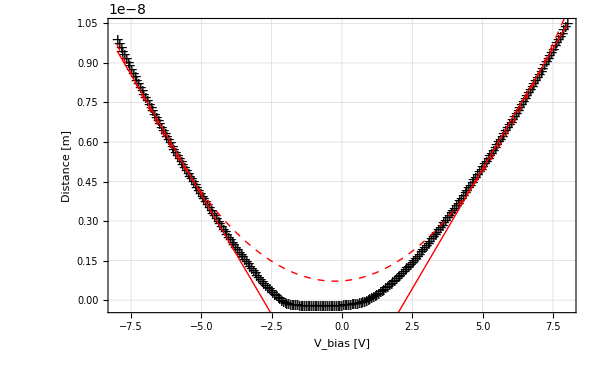

```mathematica
C77IVFwdFitTemp=Drop[C77IVFwd,{Position[C77IVFwd,-4.04705905914307][[1,1]],
Position[C77IVFwd,4.04705905914307][[1,1]]}];
C77IVFwdFit=Replace[C77IVFwdFitTemp,{xi_,yi_}->{xi,calib*yi/Zgain},2];
FitSphereC77Fwd=NonlinearModelFit[C77IVFwdFit,m Abs[U-U0]+c,{m,U0,c},U];
FitSphereC77Fwd["ParameterTable"]
NSolve[((Pi ϵ0 r*10^-9)/FGrad)^(1/2)==FitSphereC77Fwd["ParameterTable"][[1,1,2,2]],r][[1,1]]
(2FGrad)/(Pi ϵ0)FitSphereC77Fwd["ParameterTable"][[1,1,2,3]]
FitConeC77Fwd=NonlinearModelFit[C77IVFwdFit,( α ((U-U0)))^2/(4Pi ϵ0 FGrad)+c,{α,U0,c},U];
FitConeC77Fwd["ParameterTable"]
NSolve[2Pi ϵ0(ArcSinh[1/Tan[x/2]])^-1==FitConeC77Fwd["ParameterTable"][[1,1,2,2]],x,WorkingPrecision->Infinity][[1,1]]
(Pi/180)^-1*2*ArcTan[1/Sinh[(2 Pi ϵ0)/θ]]/.θ->FitConeC77Fwd["ParameterTable"][[1,1,2,2]]
Show[ListPlot[{Replace[C77IVFwd,{Vi_,ki_}->{Vi,calib*ki/Zgain},2]},PlotStyle->{Black},PlotMarkers->{"+",16}],Plot[Normal[FitSphereC77Fwd],{U,-8,8},PlotRange->Full,PlotStyle->{Thick,Red}],Plot[Normal[FitConeC77Fwd],{U,-8,8},PlotStyle->{Thick,Dashed,Red}],ImageSize->600,niceStyle2]
```

| Estimate | Standard Error | t-Statistic | P-Value
m | 1.81815×10^-9 | 6.90443×10^-12 | 263.331 | 4.13572×10^-171
U0 | -0.279054 | 0.00446055 | -62.5605 | 4.17367×10^-95
c | -4.60129×10^-9 | 4.25414×10^-11 | -108.16 | 8.27614×10^-124

r→1.54961

1.54961

0.00647324

| Estimate | Standard Error | t-Statistic | P-Value
α | 1.4732×10^-11 | 3.74067×10^-14 | 393.833 | 1.38328×10^-192
U0 | -0.27259 | 0.00587944 | -46.3632 | 9.36707×10^-80
c | 7.17343×10^-10 | 3.06535×10^-11 | 23.4017 | 3.97587×10^-47

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

x→0.0916127

5.24902

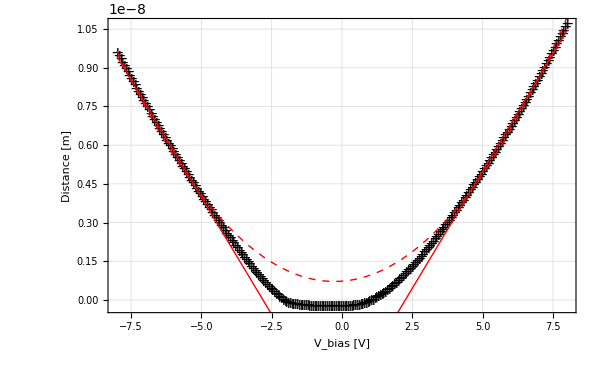

```mathematica
C77IVBwdFitTemp=Drop[C77IVBwd,{Position[C77IVBwd,-4.04705905914307][[1,1]],
Position[C77IVBwd,4.04705905914307][[1,1]]}];
C77IVBwdFit=Replace[C77IVBwdFitTemp,{xi_,yi_}->{xi,calib*yi/Zgain},2];
FitSphereC77Bwd=NonlinearModelFit[C77IVBwdFit,m Abs[U-U0]+c,{m,U0,c},U];
FitSphereC77Bwd["ParameterTable"]
NSolve[((Pi ϵ0 r*10^-9)/FGrad)^(1/2)==FitSphereC77Bwd["ParameterTable"][[1,1,2,2]],r][[1,1]]
(FGrad x^2)/(Pi ϵ0)10^9/.x->FitSphereC77Bwd["ParameterTable"][[1,1,2,2]]
(2FGrad)/(Pi ϵ0)FitSphereC77Bwd["ParameterTable"][[1,1,2,3]]
FitConeC77Bwd=NonlinearModelFit[C77IVBwdFit,( α ((U-U0)))^2/(4Pi ϵ0 FGrad)+c,{α,U0,c},U];
FitConeC77Bwd["ParameterTable"]
NSolve[2Pi ϵ0(ArcSinh[1/Tan[x/2]])^-1==FitConeC77Bwd["ParameterTable"][[1,1,2,2]],x,WorkingPrecision->Infinity][[1,1]]
(Pi/180)^-1*2*ArcTan[1/Sinh[(2 Pi ϵ0)/θ]]/.θ->FitConeC77Bwd["ParameterTable"][[1,1,2,2]]
Show[ListPlot[{Replace[C77IVBwd,{Vi_,ki_}->{Vi,calib*ki/Zgain},2]},PlotStyle->{Black},PlotMarkers->{"+",16}],Plot[Normal[FitSphereC77Bwd],{U,-8,8},PlotRange->Full,PlotStyle->{Thick,Red}],Plot[Normal[FitConeC77Bwd],{U,-8,8},PlotStyle->{Thick,Dashed,Red}],ImageSize->600,niceStyle2]
```

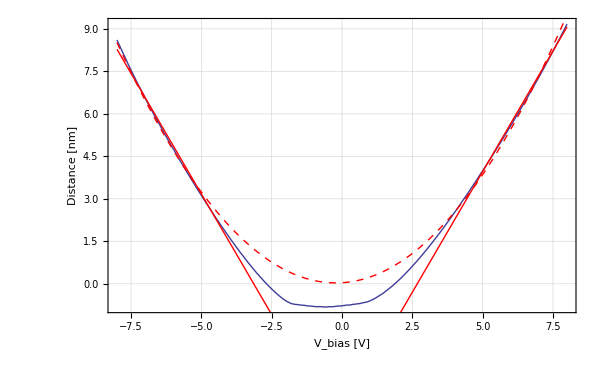

```mathematica
FitSphereC57IVFwd2=NonlinearModelFit[Replace[C57IVFwdFitTemp,{xi_,yi_}->{xi,calib*yi/15*10^9},2],m Abs[U-U0]+c,{m,U0,c},U];
FitConeC57IVFwd2=NonlinearModelFit[Replace[C57IVFwdFitTemp,{xi_,yi_}->{xi,calib*yi/15*10^9},2],( α ((U-U0)))^2/(4Pi ϵ0 FGrad)+c,{α,U0,c},U];
Show[ListLinePlot[{Replace[C57IVFwd,{Vi_,ki_}->{Vi,calib*ki/15*10^9},2]},PlotStyle->{Thick}],Plot[Normal[FitSphereC57IVFwd2],{U,-8,8},PlotRange->Full,PlotStyle->{Thick,Red}],Plot[Normal[FitConeC57IVFwd2],{U,-8,8},PlotStyle->{Thick,Dashed,Red}],ImageSize->600,
Axes->True,
Frame->True,
GridLines->Automatic,
ImageSize->600,
ImageMargins->3,
LabelStyle->{"Arial",16,Bold},
BaseStyle->{FontFamily->"Arial",FontSize->16},
FrameTicksStyle->{Directive[16,Plain],Directive[16,Plain]},
FrameStyle->Thick,
GridLinesStyle->Directive[Dashed,Gray],
AxesStyle->Directive[Thick,Dashed],
FrameLabel->{"V_bias [V]","Distance [nm]"}]
```